## TEMPLATE with MASSIVE HELP from Bob Nachbar

Thread -> a list of pairs, FROM a pair of lists 
UpTo accounts  for “taking” “more” than the length of the list

MUST EVALUATE CELLS BELOW FOR TEMPLATE TO WORK

The next two lines are doing the SAME THING in different syntax

```mathematica
DeleteCases[Take[ReverseSortBy[Thread[{VertexList[#],BetweennessCentrality[#]}],Last],UpTo[15]],{_,0.}]&/@accumulatingGraphs;
```

```mathematica
ClearAll[gleanWellConnectedPersons]
Options[gleanWellConnectedPersons]={"count"->15,"measure"->BetweennessCentrality};
gleanWellConnectedPersons[graph_,OptionsPattern[]]:=
Module[{measure,count,namesAndCentralities,sortedList,topPersons},
measure=OptionValue["measure"];
count=OptionValue["count"];
namesAndCentralities=Thread[{VertexList[graph],measure[graph]}];
sortedList=ReverseSortBy[namesAndCentralities,Last];
topPersons=Take[sortedList,UpTo[count]];
DeleteCases[topPersons,{_,0.}]
]
```

The orange colored font 
	1) The Variable depicting the SNA metric, and
	2) The SNA metric 
		are what need to change to ascertain different graph variables:
		
(The function below was suppressed because creating all of the graphs took too much time/space)
Two Examples

ClosenessCentrality

```mathematica
topConnectedPersonsByCloseness=gleanWellConnectedPersons[#,"measure"->ClosenessCentrality]&/@accumulatingGraphs;
```

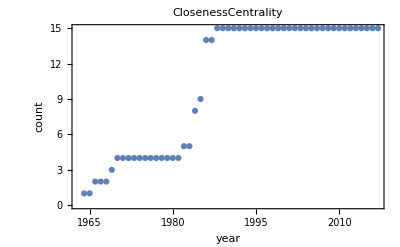

```mathematica
ListPlot[Length/@topConnectedPersonsByCloseness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->ClosenessCentrality]
```

BetweennessCentrality

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs;
```

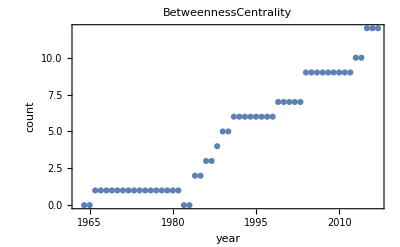

```mathematica
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->BetweennessCentrality]
```

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs
```

<|1964→{},1965→{},1966→{{David Matza,18.}},1967→{{David Matza,18.}},1968→{{David Matza,18.}},1969→{{David Matza,18.}},1970→{{David Matza,35.}},1971→{{David Matza,35.}},1972→{{David Matza,35.}},1973→{{David Matza,35.}},1974→{{David Matza,35.}},1975→{{David Matza,35.}},1976→{{David Matza,35.}},1977→{{David Matza,35.}},1978→{{David Matza,35.}},1979→{{David Matza,35.}},1980→{{David Matza,35.}},1981→{{David Matza,35.}},1982→{},1983→{},1984→{{Theda Skocpol,30.},{Manuel Castells,24.}},1985→{{Theda Skocpol,30.},{Manuel Castells,24.}},1986→{{Charles Tilly,96.},{Theda Skocpol,62.},{Manuel Castells,24.}},1987→{{Charles Tilly,96.},{Theda Skocpol,62.},{Manuel Castells,24.}},1988→{{Charles Tilly,96.},{Theda Skocpol,62.},{David Matza,35.},{Manuel Castells,24.}},1989→{{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.}},1990→{{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.}},1991→{{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},1992→{{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},1993→{{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},1994→{{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},1995→{{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},1996→{{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},1997→{{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},1998→{{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},1999→{{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.},{Gerald D. Suttles,12.}},2000→{{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.},{Gerald D. Suttles,12.}},2001→{{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.},{Gerald D. Suttles,12.}},2002→{{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.},{Gerald D. Suttles,12.}},2003→{{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.},{Gerald D. Suttles,12.}},2004→{{Mitchell Duneier,215.},{Michele Lamont,97.},{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Gerald D. Suttles,24.},{Sharon Zukin,16.}},2005→{{Mitchell Duneier,215.},{Michele Lamont,97.},{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Gerald D. Suttles,24.},{Sharon Zukin,16.}},2006→{{Mitchell Duneier,215.},{Michele Lamont,97.},{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Gerald D. Suttles,24.},{Sharon Zukin,16.}},2007→{{Mitchell Duneier,215.},{Michele Lamont,97.},{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{David Matza,35.},{Manuel Castells,24.},{Gerald D. Suttles,24.},{Sharon Zukin,16.}},2008→{{Mitchell Duneier,215.},{Michele Lamont,97.},{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{Gerald D. Suttles,36.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},2009→{{Mitchell Duneier,214.},{Michele Lamont,97.},{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{Gerald D. Suttles,36.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},2010→{{Mitchell Duneier,214.},{Michele Lamont,97.},{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{Gerald D. Suttles,36.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},2011→{{Mitchell Duneier,214.},{Michele Lamont,196.},{Charles Tilly,96.},{Theda Skocpol,62.},{Walter Korpi,38.},{Gerald D. Suttles,36.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},2012→{{Mitchell Duneier,214.},{Michele Lamont,196.},{Charles Tilly,128.},{Theda Skocpol,127.},{Walter Korpi,38.},{Gerald D. Suttles,36.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},2013→{{Michele Lamont,370.},{Mitchell Duneier,214.},{Charles Tilly,128.},{Theda Skocpol,127.},{Nancy DiTomaso,122.},{Walter Korpi,38.},{Gerald D. Suttles,36.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},2014→{{Michele Lamont,512.},{Mitchell Duneier,214.},{Nancy DiTomaso,164.},{Charles Tilly,128.},{Theda Skocpol,127.},{Walter Korpi,38.},{Gerald D. Suttles,36.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},2015→{{Michele Lamont,511.5},{Mitchell Duneier,214.},{Nancy DiTomaso,164.},{Charles Tilly,128.},{Theda Skocpol,127.},{Carla Shedd,123.5},{John Hagan,78.},{Walter Korpi,38.},{Gerald D. Suttles,36.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},2016→{{Michele Lamont,511.5},{Mitchell Duneier,214.},{Nancy DiTomaso,164.},{Charles Tilly,128.},{Theda Skocpol,127.},{Carla Shedd,123.5},{John Hagan,78.},{Walter Korpi,38.},{Gerald D. Suttles,36.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}},2017→{{Michele Lamont,511.5},{Mitchell Duneier,214.},{Nancy DiTomaso,164.},{Charles Tilly,128.},{Theda Skocpol,127.},{Carla Shedd,123.5},{John Hagan,78.},{Walter Korpi,38.},{Gerald D. Suttles,36.},{David Matza,35.},{Manuel Castells,24.},{Sharon Zukin,16.}}|>